```mathematica
Now-DateObject[{1999, 6, 11}]
```

7268. days

```mathematica
MoonPhase[Now]
```

0.01469

```mathematica
Here
```

GeoPosition[{-36.15,-71.83}]

```mathematica
GeoGraphics[Here,GeoBackground->"ReliefMap"]
```

Import::fmterr: Cannot import data as GeoTIFF format.

GeoGraphics::data: Unable to download data for ranges {{-36.3155,-35.9845},{-72.0341,-71.6259}} and zoom level 11 from the geo server ReliefMap.

-Graphics-

```mathematica
Sunset[Here,Now]-Sunrise[Here,Now]
```

628 min

```mathematica
Sunrise[Here,Now]-Sunrise[Here,Tomorrow +Quantity[1, "Days"]]+Quantity[1, "Days"]
```

-1 min

```mathematica
AirTemperatureData[Here,{DatePlus[Today, -Quantity[1, "Weeks"]],Now}]
```

TimeSeries[…]

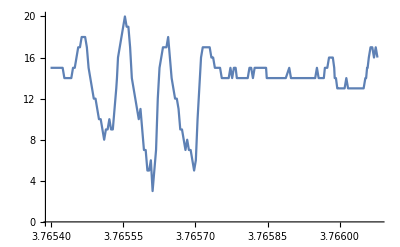

```mathematica
ListLinePlot[%]
```

```mathematica
GeoNearest["Country",Here,6]
```

{Chile,Argentina,Uruguay,Brazil,Bolivia,Paraguay}

```mathematica
GeoNearest["Volcano",Here,7]
```

GeoNearest::timeout: A network operation for GeoNearest timed out. Please try again later.

$Failed

```mathematica
EntityClass["LightColor","VisibleLight"]
```

visible light

```mathematica
EntityList[EntityClass["LightColor","VisibleLight"]]
```

{red light,orange light,yellow light,green light,cyan light,blue light,violet light}

```mathematica
Table[Blur[Rasterize[Style["hello",15]],r],{r,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
TextRecognize[{-Graphics-,-Graphics-,-Graphics-}]
```

{hello,hella,_HI}

```mathematica
(*Aplicaciones de Funciones*)
(*Unda de las mas comunes es @, que se usa, f@x, que significa f[x]*)
f@x
```

f[x]

```mathematica
(*Otra es con los BackSlash //*)
-Graphics- // EdgeDetect // ColorNegate
```

-Graphics-

```mathematica
(*Las imagenes se leen como se van aplicando*)
(*A medida que se va trabajando con Wolfram Language,se acaba por usar todo el tiempo una notación muy poderosa,a saber, /@,que significa “aplicar a cada elemento”.*)
f/@{2,4,5}
```

{f[2],f[4],f[5]}

```mathematica
Framed[{x,y,z}]
```

{x,y,z}

```mathematica
Framed/@{x,y,z}
```

{x,y,z}

```mathematica
Range[3]
```

{1,2,3}

```mathematica
Range/@{1,2,3,4,5}
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

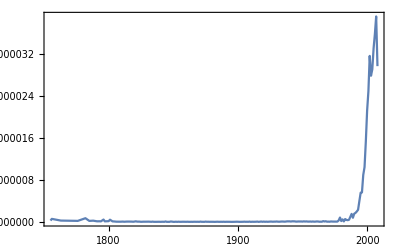

```mathematica
DateListPlot[WordFrequencyData["internet","TimeSeries"],PlotRange->All]
```

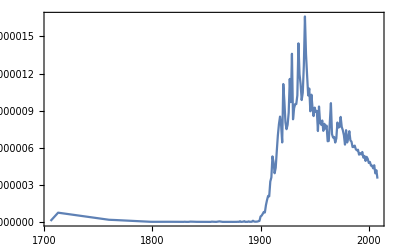

```mathematica
DateListPlot[WordFrequencyData["automobile","TimeSeries"],PlotRange->All]
```

```mathematica
GeoListPlot[Entity["Country","France"],GeoRange->EntityClass["Country","Europe"],GeoBackground->"ReliefMap"]
```

GeoGraphics::invgr: Europe is not a valid GeoRange specification.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[$Failed].

General::stop: Further output of Reverse::normal will be suppressed during this calculation.

Take::take: Cannot take positions 214 through 700 in {{Reverse[$Failed],-84,-84,-84,-85,-86,-86,-86,-86,-86,-86,-87,-88,-87,-86,-86,-87,-88,-88,-87,-86,-86,-87,-88,-88,-88,-88,-88,-86,-86,-86,-86,-86,-87,-90,-92,-91,-91,-92,-92,-92,-92,-92,-92,-93,-93,-90,-85,-81,-86,«463»},«49»,«208»}.

GeoGraphics::data: Unable to download data for ranges {{40.8795,51.576},{-5.51316,10.2782}} and zoom level 6 from the geo server ReliefMap.

```mathematica
ImageIdentify[-Graphics-,All,10]
```

{whortleberry,blueberry,Alaskan malamute,berry,northern fur seal,guadalupe fur seal,California sea lion,Australian sea lion,Steller sea lion,sled dog}

```mathematica
Blur[#,5]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Rotate[#,90 Degree]&/@{"one","two","three"}
```

{one,two,three}

```mathematica
Style["hello",20,#]&/@{Red,Orange,Blue,Purple}
```

{hello,hello,hello,hello}

```mathematica
{#,StringLength[WikipediaData[#]]}&@{"Apple","Pear","Lemon","Cats"}//Grid
```

Apple | Pear | Lemon | Cats
31417 | 11586 | 9121 | 62586

```mathematica
Style[#,Hue[#/10],5 #]&/@IntegerDigits[2^30]
```

{1,0,7,3,7,4,1,8,2,4}

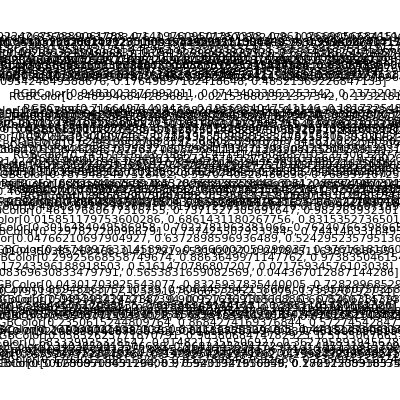

```mathematica
FeatureSpacePlot@RandomColor[100]
```

```mathematica
Table[Rasterize[FromLetterNumber[n]],{n,26}]//FeatureSpacePlot
```

```mathematica
LanguageIdentify["ajatella"]
```

```mathematica
Classify["Language"]["ajatella"]
```

$Aborted

```mathematica
Classify["Language"]["ajatella"]

GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[2,"Miles"]]]
```

Classify::dlfail: Error downloading or installing the classifier named Language.

QuantityArray[…]

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[2,"Miles"]]],MeshStyle->None]
```

-Graphics3D-

ListContourPlot::arrayerr: … must be a valid array.

```mathematica
GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[2,"Miles"]]]//ListContourPlot
```

-Graphics-

```mathematica
Histogram3D@ImageData[Graphics@Style["W",200],"Byte"]
```

Histogram3D::ldata: {{{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},«19»,{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},«310»},«49»,«309»} is not a valid dataset or list of datasets.

Histogram3D[{{{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},331,{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84},{255,84,84}},358}]
 |  |  |  |

```mathematica
Histogram3D
```

{-Graphics-}